## Setup

```mathematica
Clear["Global`*"];
```

```mathematica
LaunchKernels[4];
```

## Utility Functions

The grid of x points in the region of the support of the potential

```mathematica
xgrid[p_]:=Module[{a,b,n,m, h,xs},
a=p["a"];
b=p["b"];
n=p["n"];
m=p["m"];
h = p["h"];

xs = Table[x,{x,a,b,h}]//N;

Return[xs];
]
```

The grid of x points in the entire region including some to the left of the support of the potential for determining the value of T.

```mathematica
xgridFull[p_]:=Module[{a,b,n,m, h,xs},
a=p["a"];
b=p["b"];
n=p["n"];
m=p["m"];
h = p["h"];

xs = Table[x,{x,a-m*h,b,h}]//N;

Return[xs];
]
```

```mathematica
kGrid[p_]:=Module[{kmin,kmax,numk,kh},
kmin=p["kmin"];
kmax=p["kmax"];
numk = p["numk"];
kh = (kmax-kmin)/(numk-1);

Return[Table[k,{k,kmin,kmax,kh}]];
];
```

```mathematica
yvec[k_,p_]:=Module[{n,m, h,cDiffCoeffs,numNonzero, nonZeroElements},
n=p["n"];
m=p["m"];
h = p["h"];

cDiffCoeffs={1,-2,1};

nonZeroElements={
n+m->-cDiffCoeffs[[1]],
n+m+1->-1*(
cDiffCoeffs[[1]]*Exp[Sqrt[2]*I*k*h]+
cDiffCoeffs[[2]]+2*h^2*k^2)
};

Return[SparseArray[nonZeroElements,{n+m+1}]];
]
```

```mathematica
yvecKVec[kVec_,p_]:=Table[yvec[k,p],{k,kVec}]
```

```mathematica
D2Matrix[p_]:= Module[{n,m,cDiffCoeffs,bands},
n=p["n"];
m=p["m"];

cDiffCoeffs={1,-2,1};

bands=Table[Band[{1,i}]->cDiffCoeffs[[i]],{i,1,Length[cDiffCoeffs]}];

Return[SparseArray[bands,{1+n+m, 1+n+m}]];
];
```

```mathematica
EMatrix[k_,p_]:=Module[{ n,m, h, band},
n=p["n"];
m=p["m"];
h = p["h"];

(*band = Band[{1,3}]->2*h^2*k^2;*)
band = Band[{1,2}]->2*h^2*k^2;
Return[SparseArray[band,{1+n+m, 1+n+m}]];
];
```

```mathematica
EMatrixKVec[kVec_,p_]:=Table[EMatrix[k,p],{k,kVec}]
```

```mathematica
VMatrix[V_,Vparams_,SEDict_]:=Module[{xg,n,m, h, u1V, matV},
xg=xgrid[SEDict][[2;;-1]];
n=SEDict["n"];
m=SEDict["m"];
h =SEDict["h"];

u1V=Band[{m+1,m+2}]->2*h^2*V[xg,Vparams];
matV = SparseArray[u1V,{1+n+m,1+n+m}];

Return[matV];
];
```

## Solve Schrodinger equation

```mathematica
SchrEqOfV[V_,VParams_, SEDict_,kVec_,D2_,EMatrixVector_,yVector_]:=Module[{VV, soln},
VV = VMatrix[V,VParams, SEDict];

soln = Table[{
kVec[[i]],
LinearSolve[D2-VV+EMatrixVector[[i]], yVector[[i]],Method->"Banded"]
},{i,1, Length[kVec]}];
Return[soln];
];
```

```mathematica
TofV[k_,x1_,x2_,SEsol1_,SEsol2_]:=Module[{},
Exp[I*Sqrt[2]*k*x2]*(1-Exp[-I*2*Sqrt[2]*k*(x2-x1)])/
(SEsol2-SEsol1*Exp[-I*Sqrt[2]*k*(x2-x1)])
];
```

```mathematica
TofVVec[V_,VParams_, SEDict_,kVec_,D2_,EMatrixVector_,yVector_]:=
Module[{step,solk,xgf,x1,x2,Tk},
step=SEDict["TCalcStep"];
solk=SchrEqOfV[V,VParams,SEDict,kVec,D2,EMatrixVector,yVector];
xgf=xgridFull[SEDict];
x1=xgf[[1]];
x2=xgf[[step]];

Tk=Table[{
sol[[1]], 
TofV[sol[[1]],x1,x2, sol[[2,1]],sol[[2,step]]]
},
{sol,solk}];

Return[Tk];
]
```

## Define Cost Function

```mathematica
Cost[T_, TGoal_, SEDict_,weights_:Table[1,{i,1,Length[T_]}]]:=
Module[{temp,cost},

(*Calculate the cost function*)
cost = Sum[
weights[[i]]*(T[[i,2]]-TGoal[[i,2]])^2,
{i,1,Length[T]}] /
 Sum[weights[[i]],{i,1,Length[T]}] ;
Return[cost];
];
```

```mathematica
CostTemp[T_, TGoal_, SEDict_,weights_:Table[1,{i,1,Length[T_]}]]:=
Module[{temp,cost},
temp=SEDict["temp"];

(*Calculate the cost function*)
cost = Sum[weights[[i]]*Exp[-T[[i,1]]^2/(2*temp)]/(√(2 temp Pi))*(T[[i,2]]-TGoal[[i,2]])^2,
{i,1,Length[T]}]/
Sum[weights[[i]]*Exp[-T[[i,1]]^2/(2*temp)]/(√(2 temp Pi)),{i,1,Length[T]}] ;

Return[cost];
];
```

```mathematica
CostConstraint[ErrFunc_, Vpars_,SEDict_]:=Module[{alpha},
alpha=SEDict["alpha"];
alpha * ErrFunc[Vpars,SEDict]
]
```

## Search for the potential

```mathematica
BackgroundWeights[k_]:=Sqrt[Sinh[Pi Sqrt[2]k]^2/(Sinh[Pi Sqrt[2]k]^2+Cosh[Pi Sqrt[7]/2]^2)]
```

```mathematica
CustomStepMonitor[TGoal_,Vfunc_,Vpars_,SEDict_,kVec_ ,costFunction_,d2_,eMatrix_,yvec_,weights_:Table[1,{i,1,Length[TGoal_]}]]:=
Module[{tvec,cost,PlotA,PlotB},
tvec=TofVVec[Vfunc, Vpars,SEDict,kVec,d2,eMatrix,yvec];
cost=costFunction[Abs[tvec], TGoal, SEDict,weights];

(*ALERT: very bad programming!!!*)
If[cost≠lastCost,
Print["Cost: ", cost];
Print["Params: ",Vpars]; 

PlotA=Plot[Vfunc[x,Vpars],{x,SEDict["a"],SEDict["b"]},PlotRange->All];
PlotB=ListPlot[{TGoal,Abs[tvec]},PlotRange->All,PlotLabel->"Cost: "<>ToString[cost]];

Print[GraphicsRow[{PlotA,PlotB}, ImageSize->Large]]
];

lastCost=cost;
]
```

```mathematica
SearchPotential [
TGoal_,Vfunc_,Vpars_,parConstrs_,SEDict_,kVec_, costFunction_,errFunction_,
weights_:Table[1,{i,1,Length[TGoal_]}],
method_:{
"DifferentialEvolution", 
"Tolerance"->0.1,
"PostProcess"->False,
"PenaltyFunction"->Function[{d,i},d*10^(2)], 
"ScalingFactor"->0.75,
 "CrossProbability"->0.5,
"RandomSeed"->3
}
]:=
Module[{VparsFlat, soln,d2mat,emat,yyvec,lastCost},
VparsFlat=Flatten[Vpars];
d2mat = D2Matrix[SEDict];
emat=EMatrixKVec[kVec,SEDict];
yyvec=yvecKVec[kVec,SEDict];

lastCost=1000;

soln=NMinimize[{
Hold[
costFunction[Abs[TofVVec[Vfunc, Vpars,SEDict,kVec,d2mat,emat,yyvec]], TGoal,SEDict,weights]+
CostConstraint[errFunction, Vpars,SEDict]
],
parConstrs
},
VparsFlat, 
Method->method, 
AccuracyGoal->2,
PrecisionGoal->2,
MaxIterations->500,
StepMonitor:> Hold[Catch[CustomStepMonitor[TGoal, Vfunc,Vpars,SEDict,kVec,costFunction,d2mat,emat,yyvec,weights]]]
];

Return[soln];
]
```

## Refine a potential

```mathematica
RefinePotential [
TGoal_,Vfunc_,Vpars_,startPars_,parConstrs_,SEDict_,kVec_, costFunction_,errFunction_,
weights_:Table[1,{i,1,Length[TGoal_]}]
]:=
Module[{VparsFlat,startParsFlat, parsstart,soln,d2mat,emat,yyvec,lastCost},
(*Debug: print inputs*)
Print[TGoal];
Print[Vfunc];
Print[Vpars];
Print[startPars];
Print[parConstrs];
Print[SEDict];
Print[kVec];
Print[costFunction];
Print[errFunction];

(*Precalculate reused values*)
VparsFlat=Flatten[Vpars];
d2mat = D2Matrix[SEDict];
emat=EMatrixKVec[kVec,SEDict];
yyvec=yvecKVec[kVec,SEDict];

Print[VparsFlat];
Print[d2mat];
Print[emat];
Print[yyvec];

(*Setup minimization params*)
startParsFlat = Flatten[startPars];
parsstart=Table[{VparsFlat[[i]],startParsFlat[[i]]},{i,1,Length[VparsFlat]}];
lastCost=1000;

(*Find the minimum*)
soln=FindMinimum[
{
Hold[
costFunction[
Abs[TofVVec[Vfunc, Vpars,SEDict,kVec,d2mat,emat,yyvec]], 
TGoal,
SEDict,
weights
]+
CostConstraint[errFunction, Vpars,SEDict]
]
, 
parConstrs
},
parsstart, 
AccuracyGoal->2,
PrecisionGoal->2,
MaxIterations->500(*,
StepMonitor:> Hold[Catch[CustomStepMonitor[TGoal, Vfunc,Vpars,SEDict,kVec,costFunction,d2mat,emat,yyvec,weights]]]*)
];

Return[soln];
]
```

## Define potentials

```mathematica
VGauss[x_,params_]:=Module[{pot,A,x0,sigma},
A=params[[1]];
x0=params[[2]];
sigma=params[[3]];

pot = A*Exp[-(x-x0)^2/2/sigma];

Return[pot];
];
```

```mathematica
VGaussN[x_,params_]:=Module[{pot},
pot=Sum[VGauss[x,pars],{pars,params}];
Return[pot];
];
```

```mathematica
VGaussL2Err[params_,SEDict_]:=Module[{pot,A,x0,σ,a,b,Vout},
A=params[[1]];
x0=params[[2]];
σ=params[[3]];
a=SEDict["a"];
b=SEDict["b"];

Vout=√(π/2) A √σ (Erfc[(-a+x0)/(√2 √σ)]+Erfc[(b-x0)/(√2 √σ)]);

Return[Abs[Vout]^2];
];
```

```mathematica
VGaussL2ErrN[params_,SEDict_]:=Module[{pot},
pot=Sum[VGaussL2Err[pars,SEDict],{pars,params}];
Return[pot];
];
```

## Define the potential and search parameters

```mathematica
SEDict = Association["a"->-10, "b"->10,"n"->500,"m"->100,"kmin"->0.01,"kmax"->2.001,"numk"->100, "TCalcStep"->25, "temp"->0.5, "alpha"->10];
SEDict["h"]=(SEDict["b"]-SEDict["a"])/SEDict["n"];
kgrid = kGrid[SEDict];
```

```mathematica
VGaussL2ErrN[{{1,-2,1.5},{-2,5,3}},SEDict]
```

0.000285588

## “k=1 single-comb” 3 gaussians

### Define target T-profile and weights:

```mathematica
TFunc[k_,a_,b_]:=(1+(k-a)^2/b^2)^(-1)
```

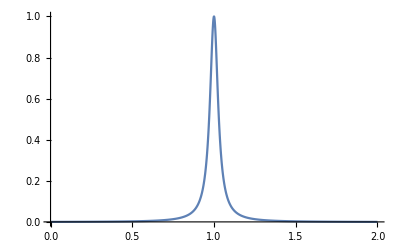

```mathematica
a=1;b=0.03;
Plot[TFunc[k,a,b],{k,0,2}, PlotRange->Full]
```

```mathematica
TTarget=Table[{k,TFunc[k,a,b]},{k,kgrid}];
```

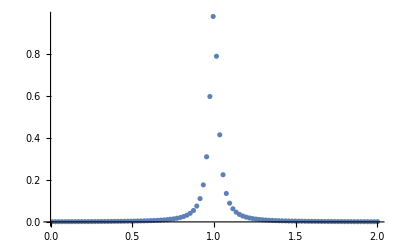

```mathematica
ListPlot[TTarget,PlotRange->Full]
```

```mathematica
kWeights=Table[BackgroundWeights[k]+TFunc[k,a,b],{k,kgrid}]^4;
```

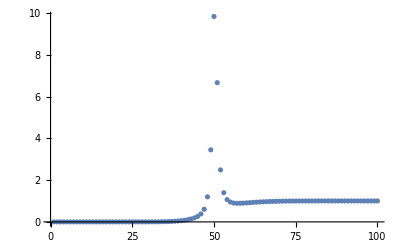

```mathematica
ListPlot[kWeights,PlotRange->All]
```

### Minimize

```mathematica
(*solGaussN=
SearchPotential [
TTarget,
VGaussN,
{{A1,x01,sigma1},
{A2,x02,sigma2},
{A3,x03,sigma3}},
{sigma1>0.01,
sigma2>0.01, 
sigma3>0.01,
x01+x02+x03==0
},
SEDict,
kgrid,
Cost,
VGaussL2ErrN,
kWeights]*)
```

### Refine the solution

```mathematica
pars = {{A1,x01,sigma1},
{A2,x02,sigma2},
{A3,x03,sigma3}}
(*startPars=pars/.solGaussN[[2]]*)
startPars={{-2.6525217812173416,0.7463163004896508,2.14055446512108},{34.906960393155295,0.3040125224809257,0.010000551410141934},{36.17475033052425,-1.0503288229705765,0.01}}
```

{{A1,x01,sigma1},{A2,x02,sigma2},{A3,x03,sigma3}}

{{-2.65252,0.746316,2.14055},{34.907,0.304013,0.0100006},{36.1748,-1.05033,0.01}}

```mathematica
RefinePotential [
TTarget,
VGaussN,
pars,
startPars,
{sigma1>0.01,
sigma2>0.01, 
sigma3>0.01,
x01+x02+x03==0
},
SEDict,
kgrid,
Cost,
VGaussL2ErrN,
kWeights]
```

{{0.01,0.000917431},{0.0301111,0.000955836},{0.0502222,0.000996702},{0.0703333,0.00104025},{0.0904444,0.00108671},{0.110556,0.00113635},{0.130667,0.00118947},{0.150778,0.0012464},{0.170889,0.00130752},{0.191,0.00137325},{0.211111,0.00144405},{0.231222,0.00152048},{0.251333,0.00160313},{0.271444,0.00169271},{0.291556,0.00179},{0.311667,0.00189592},{0.331778,0.00201153},{0.351889,0.00213803},{0.372,0.00227684},{0.392111,0.00242962},{0.412222,0.00259828},{0.432333,0.00278512},{0.452444,0.00299285},{0.472556,0.00322468},{0.492667,0.00348449},{0.512778,0.00377698},{0.532889,0.00410785},{0.553,0.0044841},{0.573111,0.00491443},{0.593222,0.00540969},{0.613333,0.0059836},{0.633444,0.00665371},{0.653556,0.00744271},{0.673667,0.0083804},{0.693778,0.0095065},{0.713889,0.0108749},{0.734,0.01256},{0.754111,0.0146672},{0.774222,0.0173492},{0.794333,0.0208339},{0.814444,0.0254735},{0.834556,0.0318338},{0.854667,0.0408686},{0.874778,0.0542803},{0.894889,0.0753242},{0.915,0.110769},{0.935111,0.176106},{0.955222,0.309805},{0.975333,0.596641},{0.995444,0.977461},{1.01556,0.788108},{1.03567,0.414343},{1.05578,0.224374},{1.07589,0.135153},{1.096,0.088968},{1.11611,0.0625791},{1.13622,0.046257},{1.15633,0.0355168},{1.17644,0.0280963},{1.19656,0.0227652},{1.21667,0.018811},{1.23678,0.0157995},{1.25689,0.0134545},{1.277,0.0115936},{1.29711,0.0100925},{1.31722,0.00886438},{1.33733,0.00784698},{1.35744,0.00699483},{1.37756,0.00627404},{1.39767,0.005659},{1.41778,0.00513001},{1.43789,0.00467176},{1.458,0.00427221},{1.47811,0.00392174},{1.49822,0.00361264},{1.51833,0.00333866},{1.53844,0.00309467},{1.55856,0.00287646},{1.57867,0.00268053},{1.59878,0.00250393},{1.61889,0.00234422},{1.639,0.0021993},{1.65911,0.00206741},{1.67922,0.00194703},{1.69933,0.00183686},{1.71944,0.00173578},{1.73956,0.00164281},{1.75967,0.00155711},{1.77978,0.00147795},{1.79989,0.00140466},{1.82,0.0013367},{1.84011,0.00127355},{1.86022,0.00121477},{1.88033,0.00115996},{1.90044,0.00110878},{1.92056,0.00106092},{1.94067,0.00101608},{1.96078,0.000974032},{1.98089,0.000934538},{2.001,0.000897397}}

VGaussN

{{A1,x01,sigma1},{A2,x02,sigma2},{A3,x03,sigma3}}

{{-2.65252,0.746316,2.14055},{34.907,0.304013,0.0100006},{36.1748,-1.05033,0.01}}

{sigma1>0.01,sigma2>0.01,sigma3>0.01,x01+x02+x03==0}

<|a→-10,b→10,n→500,m→100,kmin→0.01,kmax→2.001,numk→100,TCalcStep→25,temp→0.5,alpha→10,h→1/25|>

{0.01,0.0301111,0.0502222,0.0703333,0.0904444,0.110556,0.130667,0.150778,0.170889,0.191,0.211111,0.231222,0.251333,0.271444,0.291556,0.311667,0.331778,0.351889,0.372,0.392111,0.412222,0.432333,0.452444,0.472556,0.492667,0.512778,0.532889,0.553,0.573111,0.593222,0.613333,0.633444,0.653556,0.673667,0.693778,0.713889,0.734,0.754111,0.774222,0.794333,0.814444,0.834556,0.854667,0.874778,0.894889,0.915,0.935111,0.955222,0.975333,0.995444,1.01556,1.03567,1.05578,1.07589,1.096,1.11611,1.13622,1.15633,1.17644,1.19656,1.21667,1.23678,1.25689,1.277,1.29711,1.31722,1.33733,1.35744,1.37756,1.39767,1.41778,1.43789,1.458,1.47811,1.49822,1.51833,1.53844,1.55856,1.57867,1.59878,1.61889,1.639,1.65911,1.67922,1.69933,1.71944,1.73956,1.75967,1.77978,1.79989,1.82,1.84011,1.86022,1.88033,1.90044,1.92056,1.94067,1.96078,1.98089,2.001}

Cost

VGaussL2ErrN

{A1,x01,sigma1,A2,x02,sigma2,A3,x03,sigma3}

SparseArray[<1800>, {601, 601}]

{SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}],SparseArray[<600>, {601, 601}]}

{SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}],SparseArray[<2>, {601}]}

## “Low pass quantum filter”

```mathematica
TofKGoalCool=Table[{k,HeavisideTheta[0.5-k]},{k,kgrid}];
```

```mathematica
weightsofKGoalCool=Table[(1-0.5/2)*HeavisideTheta[-k+0.5]+0.5/2*HeavisideTheta[k-0.5],{k,kgrid}];
```

```mathematica
(*SearchPotential [
TofKGoalCool,
VGaussN,
{{A1,x01,sigma1},{A2,x02,sigma2}},
{sigma1>0.01,sigma2>0.01,x01+x02==0, x02≥0},
SEDict,
kgrid,
weightsofKGoalCool]*)
```

## “High-pass quantum filter”

```mathematica
TofKGoalCool=Table[{k,HeavisideTheta[k-0.5]},{k,kgrid}];
weightsofKGoalCool=Table[(1-0.5/2)*HeavisideTheta[-k+0.5]+0.5/2*HeavisideTheta[k-0.5],{k,kgrid}];
```

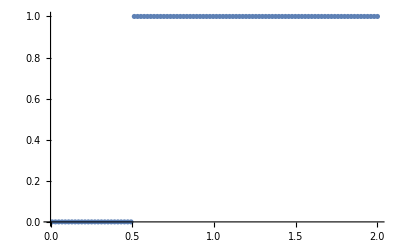

```mathematica
ListPlot[TofKGoalCool]
```

```mathematica
(*solGaussN=
SearchPotential [
TofKGoalCool,
VGaussN,
{{A1,x01,sigma1},{A2,x02,sigma2}},
{sigma1>0.01,sigma2>0.01,x01+x02==0, x02≥0},
SEDict,
kVecTest]*)
```

## “Low-pass quantum filter” 3 gaussians

```mathematica
TofKGoalCool=Table[{k,HeavisideTheta[-k+0.5]},{k,kgrid}];
weightsofKGoalCool=Table[(1-0.5/2)*HeavisideTheta[-k+0.5]+0.5/2*HeavisideTheta[k-0.5],{k,kgrid}]
```

{0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25}

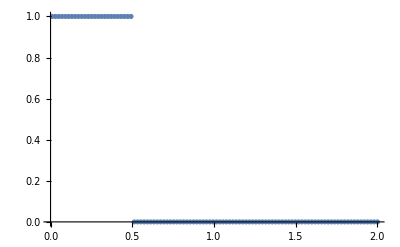

```mathematica
ListPlot[{TofKGoalCool}]
```

```mathematica
(*solGaussN=
SearchPotential [
TofKGoalCool,
VGaussN,
{{A1,x01,sigma1},{A2,x02,sigma2},{A3,x03,sigma3}},
{sigma1>0.01,sigma2>0.01,sigma3>0.01,x01+x02+x03==0},
SEDict,
kVecTest,
weightsofKGoalCool]*)
```